# Three-State Markov Chain Model

## Mathematica functions for simulation of discrete hidden Markov chains

#### G. Woehlke, 2025

## Three-state Markov Chain Construction

```mathematica
CellPrint[TextCell["Reaction Scheme",CellTags->"Scheme","Subsection"]]
```

### Reaction Scheme

We consider a three-state model with the following connectivity and transition probabilities: 
  -Graphics-

```mathematica
Grid[{{"  to state →\rfrom state\r     ↓","S_1","S_2","S_3"},
{"S_1","p(k_11)=1-(p(k_12)+p(k_13))","p(k_12)=1-ⅇ^(-SubscriptBox[k, 12])","p(k_13)=1-ⅇ^(-SubscriptBox[k, 13])"},
{"S_2","p(k_21)=1-ⅇ^(-SubscriptBox[k, 21])","p(k_22)=1-(p(k_21)+p(k_23))","p(k_23)=1-ⅇ^(-SubscriptBox[k, 23])"},
{"S_3","p(k_31)=1-ⅇ^(-SubscriptBox[k, 31])","p(k_32)=1-ⅇ^(-SubscriptBox[k, 32])","p(k_33)=1-(p(k_31)+p(k_32)"}},Frame->All]
```

to state →\rfrom state\r     ↓ | S_1 | S_2 | S_3
S_1 | p(k_11)=1-(p(k_12)+p(k_13)) | p(k_12)=1-ⅇ^(-SubscriptBox[k, 12]) | p(k_13)=1-ⅇ^(-SubscriptBox[k, 13])
S_2 | p(k_21)=1-ⅇ^(-SubscriptBox[k, 21]) | p(k_22)=1-(p(k_21)+p(k_23)) | p(k_23)=1-ⅇ^(-SubscriptBox[k, 23])
S_3 | p(k_31)=1-ⅇ^(-SubscriptBox[k, 31]) | p(k_32)=1-ⅇ^(-SubscriptBox[k, 32]) | p(k_33)=1-(p(k_31)+p(k_32)

```mathematica
Unset[{p11,p12,p13,p21,p22,p23,p31,p32,p33}]  (* In case we want to reset Subscript[p, ij] *)
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
CellPrint[TextCell["Set Parameters",CellTags->"params","Subsection"]]
```

### Set Parameters

We define for our example: k12 = 5 s^-1, k21 = 0.5 s^-1, k23 = 1. s^-1, k32 = 0.1 s^-1. k13 and k31 were 0. The fastest rate is 5 s^-1 ⟷ 0.2 s transition time, hence the sampling frequency should be at least 10 s^-1 = 10 Hz.  Feel free to change!

```mathematica
k12=5.;k21=0.5;k23=1.;k32=0.5;k13=0;k31=0;
```

```mathematica
δ=10.;
```

The probabilities to observe a transition i → j in the time interval 1/δ are

```mathematica
p12=1-ⅇ^(-k12/δ);
p13=1-ⅇ^(-k13/δ);
p21=1-ⅇ^(-k21/δ);
p23=1-ⅇ^(-k23/δ);
p31=1-ⅇ^(-k31/δ);
p32=1-ⅇ^(-k32/δ);
```

If there is no transition observed, th state stays the same, i.e. the remaining probatility to one is:

```mathematica
p11=1-(p12 + p13) ;
p22= 1-(p21 + p23) ;
p33= 1-(p31 + p32) ;
```

```mathematica
tm3state={{p11,p12,p13},{p21,p22,p23},{p31,p32,p33}}
```

{{0.606531,0.393469,0.},{0.0487706,0.856067,0.0951626},{0.,0.0487706,0.951229}}

```mathematica
MatrixForm[tm3state]
```

(0.606531 | 0.393469 | 0.
0.0487706 | 0.856067 | 0.0951626
0. | 0.0487706 | 0.951229)

```mathematica
dmp=DiscreteMarkovProcess[1,tm3state]
```

DiscreteMarkovProcess[1,{{0.606531,0.393469,0.},{0.0487706,0.856067,0.0951626},{0.,0.0487706,0.951229}}]

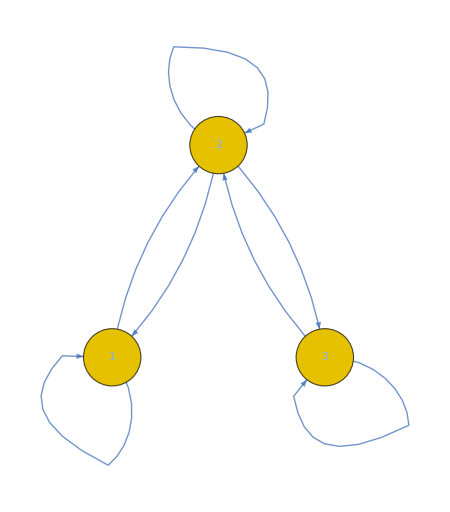

```mathematica
Graph[dmp,ImageSize->450]
```

## Simulation of the Time Series

```mathematica
CellPrint[TextCell["Create Time Series",CellTags->"timeS","Subsection"]]
```

### Create Time Series

We now are able to simulate a time sequence obeying this model:

```mathematica
hmmTimeSeries=RandomFunction[dmp,{0,500}];
```

```mathematica
Manipulate[ListPlot[hmmTimeSeries,
Joined->join,GridLines->{None,{1,2,3}},
PlotLabel->"three-state HMM",LabelStyle->Directive[fs, Black],
PlotStyle->{color,Thickness[thn]},
(*Axes->{True,False},*)
Ticks->{Automatic,{1,2,3}},
AxesLabel->{"observation \rframes","state"},
AspectRatio->1/3,ImageSize-> is],
{color,{Blue,RGBColor[0.5,0.5,0.85],Black,Darker[Gray],Orange,Red,Darker[Green]}},
{{fs,21,"font size"},{14,18,21,24,28}},
{{join,False,"join points"},{True,False}},
{{thn,0.005,"line thickness"},0.001,0.025},
{{is,720,"image size"},{450,650,720,950,1080}}]
```

```mathematica
Button["Enter new kinetic parameters",NotebookLocate[{"MathCode_19_HMM-3state.nb","params"}],Background->LightYellow]
```

Enter new kinetic parameters

## Statistics of State Population

The distribution of dwell times shows which states are long-lived, indicating fast rates that lead to that state, and slow rates leaving it.

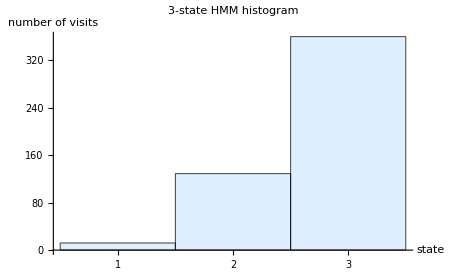

```mathematica
Histogram[hmmTimeSeries,ChartStyle->{LightBlue},PlotLabel->"3-state HMM histogram",LabelStyle->Directive[21, Black],(*AxesLabel->"number of visits"*)AxesLabel->{"state","number of visits"},Ticks->{{1,2,3},Automatic},ImageSize-> 450]
```

```mathematica
Button["Create new time series",NotebookLocate[{"MathCode_19_HMM-3state.nb","timeS"}],Background->LightYellow]
```

Create new time series

```mathematica
Button["Enter new parameters",NotebookLocate[{"MathCode_19_HMM-3state.nb","params"}],Background->LightYellow]
```

Enter new parameters

```mathematica
Button["Go to reaction scheme",NotebookLocate[{"MathCode_19_HMM-3state.nb","Scheme"}],Background->LightYellow]
```

Go to reaction scheme